## notes tbd

- SessionScope needs to be on context path
- needs / get
- bookmarks
- session dialog preview
- language support
- ImageSizeCache
- encode injected


- encryption

## READ.ME

User's job is:

- to provide code in "notebook / session methods" 
  this is the place to define your ui elements or methods. you can use everything defined in "session variables" too
  app independent dependencies should be put explicitely in Initialization, find the line with Needs["PacletManager`"]
    
- to export sessions symbols in "session variables" 
  this is a place to mention variables used by methods etc, it has a separate context to be ableto easily 'bookmark'/load session (*feature tbd*)

## build script

It should not be edited unless really needed. The place for app code is in sections below this one.
This one will be converted into a function in future.

```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\Kuba\IdeaProjects\NotebookApps

```mathematica
PacletDirectoryAdd@NotebookDirectory[]
```

{C:\Users\Kuba\IdeaProjects\NotebookApps\}

```mathematica
PacletFind@"NotebookApps"
```

{Paclet[NotebookApps,0.5.0,<>]}

```mathematica
Get@FileNameJoin[{NotebookDirectory[],"NotebookApps","NotebookApps.m"}]
```

```mathematica
PacletUninstall/@PacletFind["NotebookApps"]
{Null,Null}
```

## bugs

```mathematica
Transpose@Table[{i,j},{i,-1,1,.1},{j,-1,1,.1}]
```

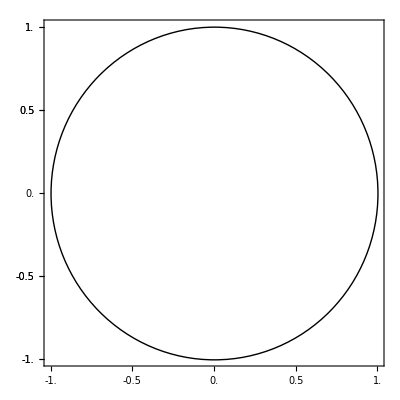

```mathematica
Framed@Pane[
Graphics[Circle[],ImageSize->Full,AspectRatio->Full,ImagePadding->22,Frame->True,FrameTicks->Transpose@Catenate@Table[{i,j},{i,-1,1,.5},{j,-1,1,.5}]]
,
AppearanceElements->"ResizeArea",
ImageSize->400{1,1/GoldenRatio},
FrameMargins->15,
BaseStyle->CacheGraphics->False
]
```

```mathematica
Framed@Pane[
Graphics[Circle[],Frame->True,ImageSize->Full,AspectRatio->Full];RandomImage[1,ImageSize->Full]
,
AppearanceElements->"ResizeArea",
ImageSize->400{1,1/GoldenRatio},
FrameMargins->15,
BaseStyle->CacheGraphics->False
]
```

-Graphics-